#### Define functions that we start with

```mathematica
fYX[y_,theta_]:=1/x
fX[x_,theta_]:=2*x/theta^2*Exp[-x^2/theta^2]
SweepCondXY[x_,y_,alpha_]:=Exp[-(x^2+y^2)/alpha^2]
```

#### Marginilize out y from the Pr(sweep|X=x,Y=y)

```mathematica
Integrate[Exp[-(x^2+y^2)/alpha^2]*1/x,{y,0,x}]
```

(alpha ⅇ^(-x^2/alpha^2) √π Erf[x/alpha])/(2 x)

Note that erf(x) is related to the incomplete gamma function erf(x) = 1-Gamma(1/2,x^2)/sqrt(Pi).

```mathematica
SweepCondX[x_,alpha_]:=(alpha ⅇ^(-x^2/alpha^2) √π Erf[x/alpha])/(2 x)
```

Make a plot for a sanity check.

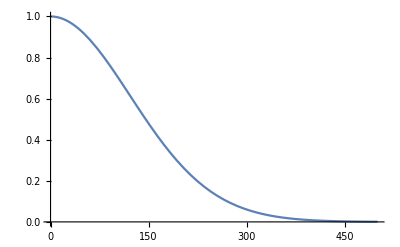

```mathematica
Plot[SweepCondX[x,200],{x,0,500}]
```

#### Now, marginilize out X from Pr(sweep|X=x)

```mathematica
Integrate[SweepCondX[x,alpha]*fX[x,theta],{x,0,Infinity}]
```

ConditionalExpression[(alpha^2 √π ArcTan[1/(√(1+alpha^2/theta^2))])/(√(π+(alpha^2 π)/theta^2) theta^2), Re[2/alpha^2+1/theta^2]≥0&&Re[alpha]>0&&Re[1/alpha^2+1/theta^2]>0]

Now, we simplify by noting that beta=alpha^2/theta^2=(cm-cwt)/cwt

```mathematica
FullSimplify[beta(√π ArcTan[1/(√(1+beta))])/(√(π+ beta*π))]
(beta ArcCot[√(1+beta)])/(√(1+beta))
```

```mathematica
Sweep[beta_]:=(beta ArcCot[√(1+beta)])/(√(1+beta))
```

We plot for a sanity check.

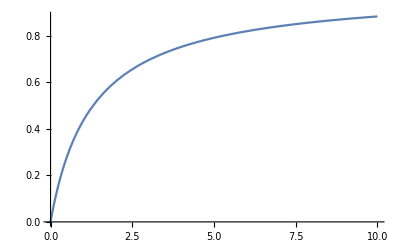

```mathematica
Plot[Sweep[beta],{beta,0,10}]
```

We plot with our approximation for comparison.

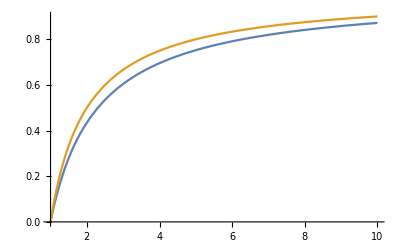

```mathematica
Plot[{(((cm-1.0)/1.0) ArcCot[√(1+((cm-1.0)/1.0))])/(√(1+((cm-1.0)/1.0))),(cm-1.0)/cm},{cm,1,10}]
```